### Define fields, potential, parameters

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->14}];
SetOptions[Plot3D,BaseStyle->{FontFamily->"Times",FontSize->14}];

ϕ={x,y};
nfReal=2;
G={{Exp[2y/r0],0},{0,1}};
Ginv=Inverse[G];

eHAsym=15*^-4;(*Asymptotic value of e_H where tanh has no effect, previously 25*)
wHAsym=484*^-2;(*previously 5, 25*)
r0val=Sqrt[2 eHAsym/wHAsym^2](*4*^-2*);
y0val=3r0val(*1*^-1*);
r1val=Sqrt[2 Exp[-2y0val/r0val]/eHAsym](*1/2*);
r2val=5*^-2;
N[r0val]
N[y0val]
N[r1val]
N[r2val]
Aval=1(*10^(-5)*);
aval=1*10^-3;
x0val=1;
yp0v=(*1*^-3*)0;

W=A Exp[x/r1](Tanh[x/r2]+1)
V=3W^2 - 2 Grad[W,ϕ].Ginv.Grad[W,ϕ](*+a^2/2(y-y0val)^2*)
```

0.0113166

0.0339497

1.81797

0.05

A ⅇ^(x/r1) (1+Tanh[x/r2])

3 A^2 ⅇ^((2 x)/r1) (1+Tanh[x/r2])^2-2 ⅇ^(-(2 y)/r0) ((A ⅇ^(x/r1) Sech[x/r2]^2)/r2+(A ⅇ^(x/r1) (1+Tanh[x/r2]))/r1)^2

### Geometric Objects

```mathematica
csymb=Simplify@Table[1/2 Sum[Ginv[[i,m]](D[G[[m,k]],ϕ[[j]]]+D[G[[j,m]],ϕ[[k]]]-D[G[[j,k]],ϕ[[m]]]),{m,nfReal}],{i,nfReal},{j,nfReal},{k,nfReal}];
riemann=Simplify@Table[D[csymb[[i,j,k]],ϕ[[l]]]-D[csymb[[i,j,l]],ϕ[[k]]]+Sum[csymb[[m,j,k]]csymb[[i,l,m]],{m,nfReal}]-Sum[csymb[[m,j,l]]csymb[[i,k,m]],{m,nfReal}],{i,nfReal},{j,nfReal},{l,nfReal},{k,nfReal}];
ricciT=Table[Sum[riemann[[i,j,i,k]],{i,nfReal}],{j,nfReal},{k,nfReal}];
ricciS=Sum[(Ginv.ricciT)[[i,i]],{i,nfReal}]
```

-2/r0^2

### Compute gradient vector and dummy gradient

```mathematica
Vgrad=Simplify@D[V,{ϕ,1}](*lower index quantity!*)
Vv=Sqrt[Vgrad.Ginv.Vgrad];
vgrad=Simplify[Vgrad/Vv];

Vh=Simplify@D[V,{ϕ,2}];
Vch=Simplify[Vh-Sum[csymb[[k,All,All]] Vgrad[[k]],{k,nfReal}]];

(*perpTensor=Ginv-Outer[Times,Evaluate[Ginv.vgrad],Evaluate[Ginv.vgrad]];*)
```

{1/(r1^3 r2^3)2 A^2 ⅇ^((2 x)/r1-(2 y)/r0) (r2+r1 Sech[x/r2]^2+r2 Tanh[x/r2]) ((-2+3 ⅇ^((2 y)/r0) r1^2) r2^2 (1+Tanh[x/r2])+4 r1 Sech[x/r2]^2 (-r2+r1 Tanh[x/r2])),(4 A^2 ⅇ^((2 x)/r1-(2 y)/r0) (r2+r1 Sech[x/r2]^2+r2 Tanh[x/r2])^2)/(r0 r1^2 r2^2)}

```mathematica
(*eV=1/2(Vgrad.Ginv.Vgrad)/V^2;*)
```

### Solve EoMs via 1st order Hamilton-Jacobi or full numerics

```mathematica
(*soln=NDSolve[{Evaluate[x'[t]==-2Evaluate[Ginv[[1,1]]D[W,x]/.{x->x[t],y->y[t]}]/.{r0->r0val,r1->r1val,r2->r2val,A->Aval}],Evaluate[y'[t]==-2Evaluate[Ginv[[2,2]]D[W,y]/.{x->x[t],y->y[t]}]/.{r0->r0val,r1->r1val,r2->r2val,A->Aval}],x[0]==x0val,y[0]==y0val},{x,y},{t,0,1*^3},MaxSteps->Infinity,WorkingPrecision->30,InterpolationOrder->All]*)
```

```mathematica
soln=NDSolve[{Evaluate[(x''[t]+3Sqrt[1/3(1/2(Exp[2y[t]/r0] x'[t]^2+y'[t]^2)+(V/.{x->x[t],y->y[t]}))]x'[t]+2/r0 y'[t]x'[t]+Exp[-2y[t]/r0](D[V,x]/.{x->x[t],y->y[t]})==0)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}],Evaluate[(y''[t]+3Sqrt[1/3(1/2(Exp[2y[t]/r0] x'[t]^2+y'[t]^2)+(V/.{x->x[t],y->y[t]}))]y'[t]-1/r0 Exp[2y[t]/r0] x'[t]^2+(D[V,y]/.{x->x[t],y->y[t]})==0)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}],x[0]==x0val,y[0]==y0val,x'[0]==(-2Exp[-2y/r0val]D[W,x]/.{x->x0val,y->y0val,r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}),y'[0]==yp0v},{x,y},{t,0,1*^3},MaxSteps->Infinity,WorkingPrecision->30,InterpolationOrder->All]
```

{{x→InterpolatingFunction[{{0, 1000.00000000000000000000000000}}, <>],y→InterpolatingFunction[{{0, 1000.00000000000000000000000000}}, <>]}}

### Plot solutions for X and Y coordinates

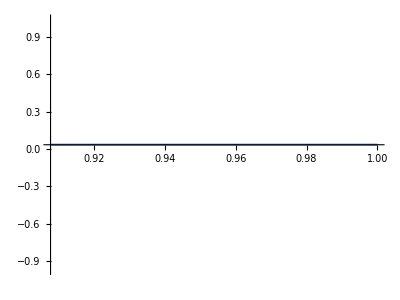

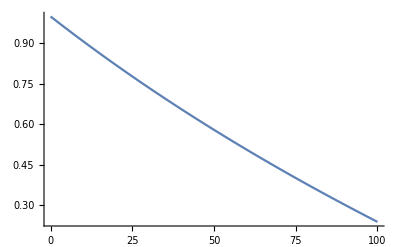

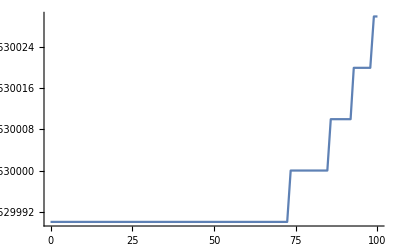

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.soln],{t,0,1*^1},PlotRange->All]
Plot[Evaluate[x[t]/.soln[[1]][[1]]],{t,0,1*^2},PlotRange->All]
Plot[Evaluate[y[t]/.soln[[1]][[2]]],{t,0,1*^2},PlotRange->All]
```

(2 ⅇ^(-(2 y)/r0) (2 r1+r2+ⅇ^((2 x)/r2) r2)^2)/((1+ⅇ^((2 x)/r2))^2 r1^2 r2^2)

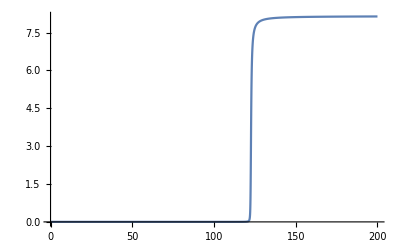

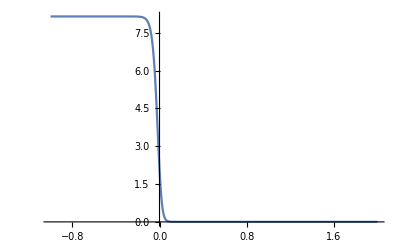

```mathematica
eH=FullSimplify[2(Ginv[[1,1]]D[W,x]^2+Ginv[[2,2]]D[W,y]^2)/W^2]
Plot[eH/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,x->Evaluate[x[t]/.soln[[1]][[1]]],y->Evaluate[y[t]/.soln[[1]][[2]]]},{t,0,2*^2}]
Plot[eH/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val},{x,-1,2}]
```

```mathematica
eH/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val,x->0.03}
```

0.477001

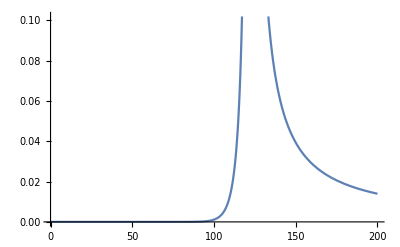

```mathematica
etaH=(xp D[eH,x](*+yp D[eH,y]*))/(W eH);
Plot[etaH/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,x->Evaluate[x[t]/.soln[[1]][[1]]],y->Evaluate[y[t]/.soln[[1]][[2]]],xp->Evaluate[x'[t]/.soln[[1]][[1]]](*,yp->Evaluate[y'[t]/.soln[[1]][[1]]]*)},{t,0,2*^2}]
```

```mathematica
etaH/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]](*,yp->Evaluate[y'[t]/.soln[[1]][[1]]]*)}
```

6.7395951088×10^-17

```mathematica
infEnd=FindRoot[Evaluate[eH/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,x->Evaluate[x[t]/.soln[[1]][[1]]],y->Evaluate[y[t]/.soln[[1]][[2]]]}]-1,{t,5*^1},WorkingPrecision->30]
```

InterpolatingFunction::dmval: Input value {1121.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1261.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{t→122.334629300111584201126989472}

```mathematica
x[t/.infEnd]/.soln[[1]][[1]]
y[t/.infEnd]/.soln[[1]][[2]]
```

0.01643611748620356024006

0.03394974532430352774468

(16 ⅇ^(-(4 y)/r0) ((A ⅇ^(x/r1) Sech[x/r2]^2)/r2+(A ⅇ^(x/r1) (1+Tanh[x/r2]))/r1)^4)/(r0^2 (ⅇ^((2 y)/r0) xp^2+yp^2))

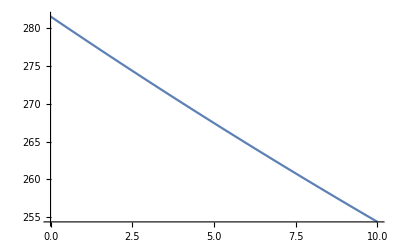

```mathematica
w2=D[V,y]^2/(Exp[2y/r0] xp^2+yp^2)
Plot[w2/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t]/.soln[[1]][[1]]],y->Evaluate[y[t]/.soln[[1]][[2]]],xp->Evaluate[x'[t]/.soln[[1]][[1]]],yp->Evaluate[y'[t]/.soln[[1]][[2]]]},{t,0,1*^1}]
```

(16 A^2 ⅇ^((2 x)/r1-(4 y)/r0) (r2+r1 Sech[x/r2]^2+r2 Tanh[x/r2])^4)/(r0^2 r1^4 r2^4 (ⅇ^((2 y)/r0) xp^2+yp^2) (1+Tanh[x/r2])^2)

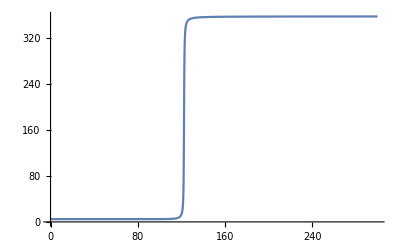

```mathematica
Simplify[w2/W^2]
Plot[(Sqrt[w2]/W)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t]/.soln[[1]][[1]]],y->Evaluate[y[t]/.soln[[1]][[2]]],xp->Evaluate[x'[t]/.soln[[1]][[1]]],yp->Evaluate[y'[t]/.soln[[1]][[2]]]},{t,0,3*^2}]
```

```mathematica
(Sqrt[w2]/W)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]],y->Evaluate[y[t/.infEnd]/.soln[[1]][[2]]],xp->Evaluate[x'[t/.infEnd]/.soln[[1]][[1]]],yp->Evaluate[y'[t/.infEnd]/.soln[[1]][[2]]]}
```

124.968262637733453763

(4 ⅇ^(-(2 y)/r0) ((A ⅇ^(x/r1) Sech[x/r2]^2)/r2+(A ⅇ^(x/r1) (1+Tanh[x/r2]))/r1)^2)/r0^2

Power::infy: Infinite expression 1/0. encountered.

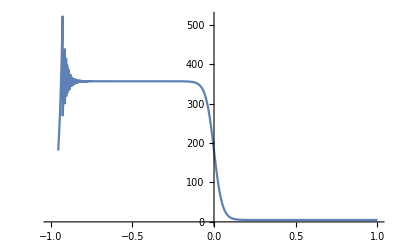

```mathematica
w2eom=D[V,y]^2/(4Exp[-2y/r0] D[W,x]^2)
Plot[(Sqrt[w2eom]/W)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val},{x,-1,x0val}]
```

```mathematica
(Sqrt[w2eom]/W)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val,x->0.03}
```

86.3096

```mathematica
(*Plot[(w2-w2eom)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t]/.soln[[1]][[1]]],y->Evaluate[y[t]/.soln[[1]][[2]]],xp->Evaluate[x'[t]/.soln[[1]][[1]]],yp->Evaluate[y'[t]/.soln[[1]][[2]]]},{t,0,10^1},WorkingPrecision->30]*)
```

```mathematica
FrontEndTokenExecute["EvaluatorAbort"];
```

$Aborted

### Calculate geodesic distance and e-folds along trajectory

```mathematica
Q[y_]:=r0^2 Exp[-2y/r0];
K[x1_,x2_,y1_,y2_]:=Sqrt[(x2-x1)^2+2(Q[y2]+Q[y1])+(Q[y2]-Q[y1])^2/(x2-x1)^2];
L[x1_,x2_,y1_,y2_]:=1/2 (x2+x1+(Q[y2]-Q[y1])/(x2-x1)+K[x1,x2,y1,y2]);
geodesic[x1_,x2_,y1_,y2_,x]:=r0 Log[r0/(Sqrt[L[x1,x2,y1,y2]-x]Sqrt[K[x1,x2,y1,y2]-L[x1,x2,y1,y2]+x])];
geodist[x1_,x2_,y1_,y2_]:=r0/2 Log[(L[x1,x2,y1,y2]-x2)/(L[x1,x2,y1,y2]-K[x1,x2,y1,y2]-x2)*(L[x1,x2,y1,y2]-K[x1,x2,y1,y2]-x1)/(L[x1,x2,y1,y2]-x1)];
```

```mathematica
geodist[x0val,x[t/.infEnd]/.soln[[1]][[1]],y0val,y[t/.infEnd]/.soln[[1]][[2]]]/.{r0->r0val,r1->r1val,r2->r2val,A->Aval}
```

0.16895461604052557112218

```mathematica
Ne=NIntegrate[Evaluate[W/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,x->Evaluate[x[t]/.soln[[1]][[1]]],y->Evaluate[y[t]/.soln[[1]][[2]]]}],{t,0,t/.infEnd}]
```

327.506

### Plot superpotential, potential

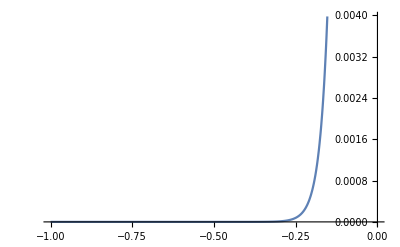

```mathematica
Plot[W/.{r0->r0val,r1->r1val,r2->r2val,A->Aval},{x,-1,0}(*,{y,-3y0val,3y0val}*)]
```

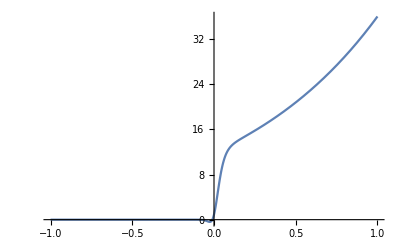

```mathematica
Plot[V/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val},{x,-1,x0val}]
```

```mathematica
V/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]],y->y0val}
```

3.5342714062905609572043808

```mathematica
N[V/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->x0val,y->y0val},30]
```

36.0366577062597020586552896706

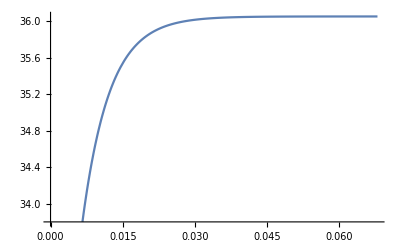

```mathematica
Plot[V/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->x0val},{y,0,2y0val}]
```

```mathematica
Vfn[x_,y_]:=Evaluate[V/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}];
```

```mathematica
Show[{Plot3D[V/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval},{x,-1,x0val},{y,-y0val,3y0val},WorkingPrecision->30],ParametricPlot3D[{x,y0val,Vfn[x,y0val]},{x,Evaluate[x[t/.infEnd]/.soln[[1]][[1]]],x0val},PlotStyle->Directive[Blue],PlotRange->All]}]
```

-Graphics3D-

### Calculate and plot ϵ_V

```mathematica
eV=1/2 Grad[V,ϕ].Ginv.Grad[V,ϕ]/V^2;
```

```mathematica
eVsimple=Simplify@eV
```

(2 ⅇ^(-(6 y)/r0) (r2+r1 Sech[x/r2]^2+r2 Tanh[x/r2])^2 (4 ⅇ^((2 y)/r0) r1^2 r2^2 (r2+r1 Sech[x/r2]^2+r2 Tanh[x/r2])^2+r0^2 ((-2+3 ⅇ^((2 y)/r0) r1^2) r2^2 (1+Tanh[x/r2])+4 r1 Sech[x/r2]^2 (-r2+r1 Tanh[x/r2]))^2))/(r0^2 r1^6 r2^6 (3 (1+Tanh[x/r2])^2-(2 ⅇ^(-(2 y)/r0) (r2+r1 Sech[x/r2]^2+r2 Tanh[x/r2])^2)/(r1^2 r2^2))^2)

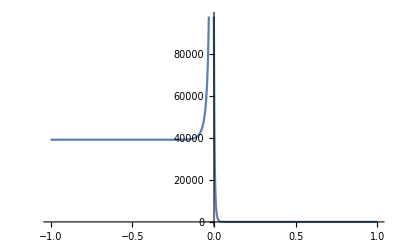

```mathematica
Plot[eVsimple/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val},{x,-1,x0val},WorkingPrecision->30]
```

```mathematica
(*FindMinimum[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val},{x,Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]},WorkingPrecision->30]*)
```

```mathematica
eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]}
```

3907.8449374538395777835059

```mathematica
N[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val,x->x0val},30]
```

0.00540817386348669327489352158553

```mathematica
N[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val,x->10x0val},30]
```

0.00540817386348668748247727332067

```mathematica
N[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->-10y0val,x->-3x0val},30]
```

3.75562326768269740229727033609×10^29

```mathematica
NSolve[Evaluate[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val}]==1 && (0≤x≤10),x]
```

{{x→0.0790314}}

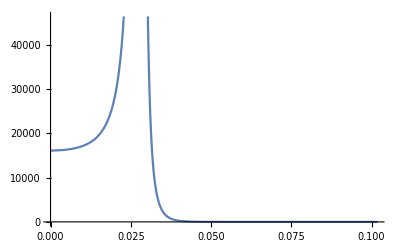

```mathematica
Plot[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]},{y,0y0val,3y0val},WorkingPrecision->30]
```

```mathematica
NSolve[Evaluate[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]}]==1 && (0≤y≤1),y]
```

{{y→0.055165890483122294258837998}}

```mathematica
N[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->0,y->2y0val},30]
```

0.0520992954980120633716001233883

```mathematica
Plot3D[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval},{x,-x0val,x0val},{y,-y0val,3y0val},WorkingPrecision->30]
```

-Graphics3D-

### Calculate and plot eigenvalues of V_(;IJ) and η_V

```mathematica
evals=(*Simplify@*)Eigenvalues[Vch];
```

```mathematica
(*evals/.{r0->r0val,r1->r1val,r2->r2val,A->Aval}*)
```

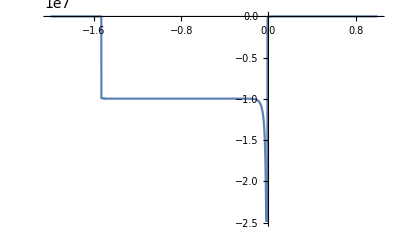

```mathematica
Plot[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val}],{x,-2,x0val},WorkingPrecision->100]
```

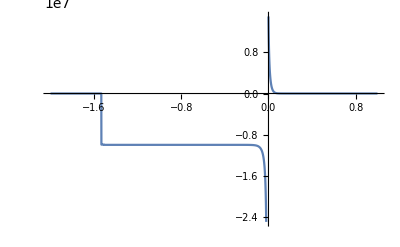

```mathematica
Plot[Evaluate[(evals[[1]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val}],{x,-2,x0val},WorkingPrecision->100]
```

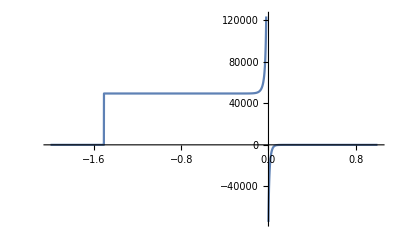

```mathematica
Plot[Evaluate[(evals[[2]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val}],{x,-2,x0val},WorkingPrecision->100]
```

```mathematica
N[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val,x->(*Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]*)x0val}],30]
```

-18.5986915576814021500016490037

```mathematica
etaBump=FindMaximum[(evals[[1]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->-y0val},{x,0},WorkingPrecision->30]
```

{215.941876572427707583778118827,{x→0.150277310990310832162336249636}}

```mathematica
N[eV/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->-y0val,x->Evaluate[x/.etaBump[[2]]]},30]
```

39690.66611608675479222277663

```mathematica
NSolve[Evaluate[(evals[[2]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val}]==-1 && (0≤x<10),x]
```

{}

```mathematica
NSolve[Evaluate[(evals[[1]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val}]==-1 && (-1≤x<-0),x]
```

{{x→-0.945523},{x→-0.940866},{x→-0.938072},{x→-0.934044},{x→-0.90187},{x→-0.901869},{x→-0.900927},{x→-0.892755},{x→-0.876932},{x→-0.835548},{x→-0.833757},{x→-0.800434},{x→-0.783975},{x→-0.768756},{x→-0.764172},{x→-0.743836},{x→-0.741149},{x→-0.735125},{x→-0.722622},{x→-0.722278},{x→-0.688339},{x→-0.672335},{x→-0.67099},{x→-0.666736},{x→-0.643939},{x→-0.638879},{x→-0.637529},{x→-0.631727},{x→-0.623467},{x→-0.622554},{x→-0.620939},{x→-0.619448},{x→-0.619274},{x→-0.616614},{x→-0.610237},{x→-0.599342},{x→-0.595567},{x→-0.595017},{x→-0.594187},{x→-0.593091},{x→-0.592682},{x→-0.590171},{x→-0.58816},{x→-0.587444},{x→-0.586457},{x→-0.584215},{x→-0.578446}}

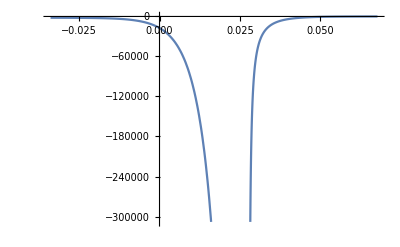

```mathematica
Plot[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]}],{y,-y0val,2y0val},WorkingPrecision->25]
```

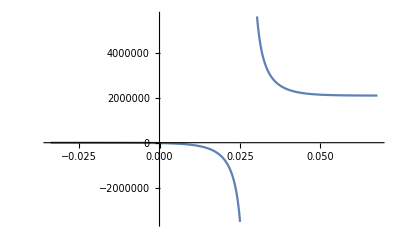

```mathematica
Plot[Evaluate[(evals[[1]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]}],{y,-y0val,2y0val},WorkingPrecision->26]
```

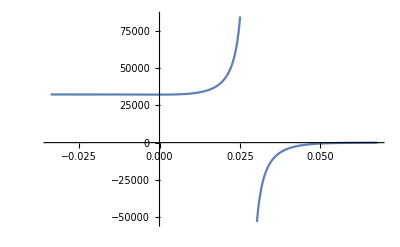

```mathematica
Plot[Evaluate[(evals[[2]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]}],{y,-y0val,2y0val},WorkingPrecision->26]
```

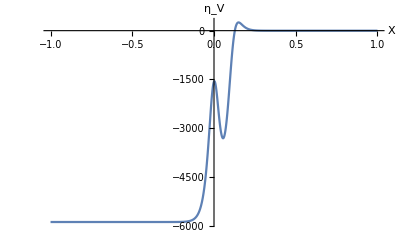

```mathematica
Plot[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->-5y0val}],{x,-1,x0val},PlotRange->All,WorkingPrecision->100,AxesLabel->{X,Subscript[η, "V"]}]
```

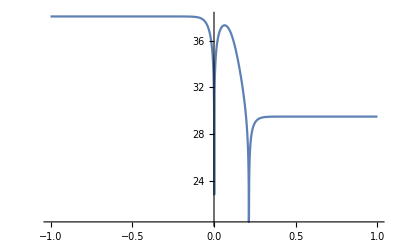

```mathematica
Plot[Log[eVsimple]/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->-5y0val},{x,-1,x0val},WorkingPrecision->30](*{x,0.20062,0.20064}*)
```

```mathematica
etaVfn2[x_,y_]:=Evaluate[(evals[[2]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}];
```

```mathematica
FrontEndExecute[FrontEndToken["EvaluatorAbort"]]
```

```mathematica
Show[{Plot3D[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}],{x,-1,x0val},{y,-y0val,2y0val},WorkingPrecision->120,PlotPoints->100,AxesLabel->{X,Y,Subscript[η, "V"]}],ParametricPlot3D[{x,y0val,etaVfn2[x,y0val]},{x,Evaluate[x[t/.infEnd]/.soln[[1]][[1]]],x0val},PlotStyle->Directive[Blue],PlotRange->All]}]
```

Min::nord: Invalid comparison with -1.45414×10^17+9.78889×10^25 ⅈ attempted.

Min::nord: Invalid comparison with -1.45414×10^17-9.78889×10^25 ⅈ attempted.

Min::nord: Invalid comparison with -1.45147×10^18+1.16028×10^25 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

-Graphics3D-

```mathematica
(*Plot3D[(evals[[1]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval},{x,-1,x0val},{y,-y0val,2y0val},WorkingPrecision->30,PlotPoints->50]*)
```

```mathematica
(*Plot3D[(evals[[2]]/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval},{x,-1,x0val},{y,-y0val,2y0val},WorkingPrecision->30,PlotPoints->50]*)
```

```mathematica
N[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->1*^1,x->x0val}],30]
```

-2.99599959293287446383711393921

```mathematica
N[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->1*^1,x->0(*Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]*)}],30]
```

-2.99939134593894765292308848455

```mathematica
N[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->-1*^2,x->x0val}],30]
```

-1.51272609513167133913897940915

```mathematica
N[Evaluate@Min[(evals/V)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->-1*^2,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]]}],30]
```

-1913.746533655945972330194

### Compute velocities along gradient and perpendicular directions

```mathematica
(*Vgrad=D[V,{ϕ,1}];
Vv=Sqrt[Vgrad.Ginv.Vgrad];
vgrad=Simplify[Vgrad/Vv];*)
vgrad/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
```

{10.5780046293745769102353285,0.8500835564591452303501543767}

```mathematica
ϕd={xp,yp};
ϕd/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
```

{-0.00945360402405842455212829855265,0}

```mathematica
(*(1/2 ϕd.G.ϕd)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

```mathematica
ϕdv=ϕd.vgrad;
ϕdv/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
```

-0.1000002671307641440647804667

```mathematica
perpTensor=Ginv-Outer[Times,Evaluate[Ginv.vgrad],Evaluate[Ginv.vgrad]];
perpVec={-vgrad[[2]],Ginv[[1,1]] vgrad[[1]]};
perpNorm=Simplify@Sqrt[perpVec.Ginv.perpVec];
perpdir=Simplify[perpVec/perpNorm];
perpdir/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
```

{-17.07438466105484992585854393,0.5266478396782533499165856593}

```mathematica
ϕdPerpNorm=ϕd.perpdir;
ϕdPerpNorm/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
ϕdPerpVec=ϕdPerpNorm perpdir;
ϕdPerpVec/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
```

0.1614144715400695686205008528

{-2.756052776936038461123235557,0.08500858272938454627071654768}

```mathematica
(*(1/2(ϕdv^2+ϕdPerpNorm^2))/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

```mathematica
ωGuess=-3ϕdPerpNorm/ϕdv;
ωGuess/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
```

4.842421210605304094393687378

### Check gradient-direction EoM

```mathematica
(*W/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

3.46673165237730767729010129517

```mathematica
(*-3W ϕdv/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

1.040022273925218449086681991

```mathematica
(*-Vv/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

-3.7478726457644786390498531911

```mathematica
(*((ϕdPerpVec.Ginv.Vch.ϕd)/Vv)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

2.708370382976222795970203346

```mathematica
(*ϕddv=-3W ϕdv-Vv+((ϕdPerpVec.Ginv.Vch.ϕd)/Vv);
ϕddv/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

0.000520011136962606007032146

### Check perp-direction EoM

```mathematica
(*-3W Ginv.ϕdPerpVec/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

{0.07104967878995921781766034285,-0.8841058334150770438070973579}

```mathematica
(*-(perpTensor.Vch.ϕd ϕdv)/Vv/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

{-0.07101415395056423919840071293,0.883663780498369517599881868}

```mathematica
(*-3W Ginv.ϕdPerpVec-ϕdv (perpTensor.Vch.ϕd)/Vv/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

{0.0000355248393949786192596299,-0.00044205291670752620721549}

```mathematica
(*-(ϕdPerpVec.Ginv.Vch.ϕd)/VvGinv.vgrad/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

{-0.0710141539505642391984007129,-2.302341127369044681211766574}

```mathematica
(*-3W Ginv.ϕdPerpVec-ϕdv (perpTensor.Vch.ϕd)/Vv-(ϕdPerpVec.Ginv.Vch.ϕd)/Vv Ginv.vgrad/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}*)
```

{-0.070978629111169260579141083,-2.30278318028575220741898206}

### Check matrix equation for ϕdPerpVec

```mathematica
mxEq=3W Vv IdentityMatrix[nfReal]+ϕdv perpTensor.Vch;
mxEqInv=Inverse[mxEq];

ϕdPerpVecTest=-ϕdv^2 mxEqInv.perpTensor.Vch.Ginv.vgrad;
ϕdPerpVecTest/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
```

{-0.00682442955969547988705335589,0.0849197081002105784496284449}

```mathematica
Ginv.ϕdPerpVec/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[0]/.soln[[1]][[1]]],y->Evaluate[y[0]/.soln[[1]][[2]]],xp->Evaluate[x'[0]/.soln[[1]][[1]]],yp->Evaluate[y'[0]/.soln[[1]][[2]]]}
```

{-0.006831571819837566930597264725,0.08500858272938454627071654768}

### Calculate ω near end of trajectory

```mathematica
eHLarge=FindRoot[Evaluate[eH/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,x->Evaluate[x[t]/.soln[[1]][[1]]],y->Evaluate[y[t]/.soln[[1]][[2]]]}]-10^-1,{t,5*^1},WorkingPrecision->30]
```

InterpolatingFunction::dmval: Input value {1121.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{t→121.723551615513772170214732959}

```mathematica
x[t/.eHLarge]/.soln[[1]][[1]]
y[t/.eHLarge]/.soln[[1]][[2]]
```

0.055341659809607241877331

0.033949745321223300053586

```mathematica
eH/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val,x->SetPrecision[0.11,30]}
```

0.005312680681246201584360023737

```mathematica
(Sqrt[w2eom]/W)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,y->y0val,x->SetPrecision[0.11,30]}
```

9.1087039900160337367081273228

```mathematica
(Sqrt[w2eom]/W)/.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval,x->Evaluate[x[t/.infEnd]/.soln[[1]][[1]]],y->Evaluate[y[t/.infEnd]/.soln[[1]][[2]]]}
```

124.9682626376259848285

### Examine the eigenvectors of covariant Hessian of potential

```mathematica
evecsMixed=Eigenvectors@Evaluate[(Ginv.Vch)//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val,x->x0val}];
evalsMixed=Eigenvalues@Evaluate[(Ginv.Vch)//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val,x->x0val}];
N[evecsMixed,30]
N[evalsMixed,30]
```

{{0.00986651238847180988518239658323,1.},{-0.251228811060184946330840360818,1.}}

{-597.598870861393344954399196884,316.172770808246390538668420964}

```mathematica
evec1Point=evecsPoint[[1]]
evec2Point=evecsPoint[[2]]
```

{0.0727112386140658029450093142,0.9973530346768933284628416066}

{0.8803859045148380731924881068,-0.4742580090326260571084037117}

```mathematica
evec1PointDir=evec1Point/Sqrt[evec1Point.G.evec1Point]//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val,x->x0val}
evec2PointDir=evec2Point/Sqrt[evec2Point.G.evec2Point]//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val,x->x0val}
```

{0.07151346222236543961570771464,0.980923581102771388289403487}

{0.3608616188479775179267538766,-0.194393744849248383779904354}

```mathematica
evec1PointDir.vgrad//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val,x->x0val}
evec2PointDir.vgrad//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val,x->x0val}
```

0.936244052210306890676634889

0.35135035890236990758989382

```mathematica
evec1PointDir.G.(ϕdPerpVec/ϕdPerpNorm)//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val,x->x0val,H->HSoln,ϕdv->ϕdvSoln}
evec2PointDir.G.(ϕdPerpVec/ϕdPerpNorm)//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,y->y0val,x->x0val,H->HSoln,ϕdv->ϕdvSoln}
```

0.3513503589023699076

-0.9362440522103068907